```mathematica
{tmax=200,δ=0.05,c=0.1,q=1.}
```

{200,0.05,0.1,1.}

InterpolatingFunction[{{0., 200.}}, <>]

InterpolatingFunction[{{0., 200.}}, <>]

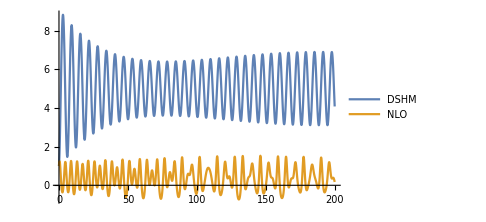

```mathematica
shm=NDSolveValue[{x''[t]+x[t]+0.05 x'[t]==5+0.1Sin[t/100]Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"]
nlo=NDSolveValue[{x''[t]+x[t]+0.01 x'[t]+0.5(x[t])^3+(x[t])^2==1+Sin[t/100]Sin[t],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"]
Plot[{(*Cos[t]+Sin[t],*)shm[t],nlo[t]},{t,0,tmax},PlotLegends->{"DSHM","NLO"},ImageSize->Medium]
```

A larger value of δ damps the mixed modes at an earlier time period.

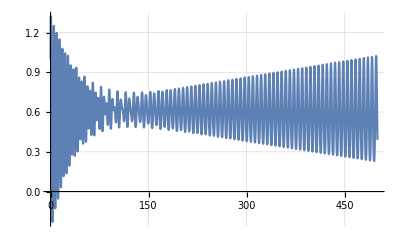

```mathematica
Module[{tmax=500,δ=0.05,c=0.,q=1.,x,t,nlo},nlo=NDSolveValue[{x''[t]+x[t]+δ x'[t]+c(x[t])^3+q(x[t])^2==1+Sin[t/1000]Sin[t/1],x[0]==1,x'[0]==1},x,{t,0,tmax},Method->"LSODA"];

Plot[nlo[t],{t,0,tmax},GridLines->Automatic]
]
```